# Conto Flow

Michael.Schreiber

```mathematica
Print@DateString[]
```

Thu 31 May 2018 17:34:55

## Goals

1. Distinguish traditional transfer events from non traditional flows between contos. 
2. Simulate blockchains which support particular protocols for related features.
3. Find concise specifications which simplify verifications of implementations.

## Approach

Changes of conto balances are recorded with block time stamps according to rates of flows. 
Types of contos are defined upon creation to model players and supply is fixed by total initial balances.
Flows with arbitrary rates change particular effects of distribution but conserve total balances.
Accumulated results of flows are recorded before changing rates.
Accumulated rates are distributed among destinations of flows.

## Install Package

```mathematica
Needs["ContoFlow`"]
```

```mathematica
<<ContoFlow`
```

```mathematica
Remove[Evaluate["ContoFlow`"<>"*"]]
```

## Two Conto Flow Example

```mathematica
{BlockTime[],Contos[],Flows[]}
```

{0,<||>,<||>}

#### New Contos

```mathematica
NewConto["a1",0,1000];NewConto["a2",1,10000];Dataset[Contos[]]
```

Dataset[<>]

#### New Flow

```mathematica
NewFlow["a1","a2",100];Dataset[Flows[]]
```

Dataset[<>]

#### Harvest

```mathematica
BlockTimePlus[]
```

1

```mathematica
Harvest["a1.a2"];Column[{Dataset[Contos[]],Dataset[Flows[]]}]
```

Dataset[<>]
Dataset[<>]

#### Pay

```mathematica
Pay["a2","a1",10]
```

```mathematica
Column[{Dataset[Contos[]],Dataset[Flows[]]}]
```

Dataset[<>]
Dataset[<>]

#### Fast Forward

```mathematica
BlockTimePlus[11]
```

12

```mathematica
Harvest["a1.a2"]
```

```mathematica
Column[{Dataset[Contos[]],Dataset[Flows[]]}]
```

Dataset[<>]
Dataset[<>]

```mathematica
Pay["a2","a1",200]
```

```mathematica
Column[{Dataset[Contos[]],Dataset[Flows[]]}]
```

Dataset[<>]
Dataset[<>]

```mathematica
Harvest["a1.a2"]
```

```mathematica
Column[{Dataset[Contos[]],Dataset[Flows[]]}]
```

Dataset[<>]
Dataset[<>]

## 100 contos

```mathematica
ContoFlowReset[]
```

```mathematica
Timing[Table[NewConto[ToString[n],Mod[n,2],10],{n,100}];]
```

{0.000932,Null}

```mathematica
Dataset[Contos[]]
```

Dataset[<>]

```mathematica
Timing[Table[Table[With[{rc=RandomInteger[{1,n}]},If[rc==n,Nothing,NewFlow[ToString[n],ToString[rc],RandomInteger[{1,10}]]]];,{m,20}],{n,1,100}];]
```

{0.050722,Null}

```mathematica
Dataset[Flows[]]
```

Dataset[<>]

```mathematica
Table[Contos[ToString[c],"bala"],{c,100}]
```

{10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}

```mathematica
Multicolumn[Keys@Flows[],36,BaseStyle->{FontSize->5}]
```

2.1 | 10.1 | 15.8 | 19.2 | 22.15 | 26.4 | 29.17 | 32.13 | 35.7 | 37.8 | 40.22 | 43.22 | 45.32 | 48.18 | 50.44 | 53.36 | 56.10 | 58.26 | 60.18 | 62.20 | 65.1 | 67.7 | 70.7 | 72.20 | 74.43 | 77.49 | 79.34 | 81.23 | 84.75 | 86.61 | 88.76 | 90.46 | 93.53 | 95.50 | 97.92 | 100.20
3.1 | 11.6 | 15.4 | 19.16 | 22.21 | 26.21 | 29.27 | 32.23 | 35.25 | 38.21 | 40.27 | 43.11 | 45.43 | 48.40 | 50.33 | 53.22 | 56.25 | 58.47 | 60.39 | 63.41 | 65.53 | 67.34 | 70.2 | 72.52 | 74.37 | 77.25 | 79.43 | 81.78 | 84.34 | 86.60 | 88.50 | 90.9 | 93.54 | 95.23 | 98.83 | 100.47
3.2 | 11.4 | 15.2 | 19.15 | 23.22 | 26.24 | 29.16 | 32.20 | 35.28 | 38.2 | 40.12 | 43.20 | 45.34 | 48.6 | 50.2 | 53.9 | 56.39 | 58.35 | 60.12 | 63.19 | 65.23 | 67.19 | 70.37 | 72.40 | 74.24 | 77.16 | 79.70 | 81.44 | 84.38 | 86.36 | 88.70 | 90.28 | 93.27 | 95.80 | 98.92 | 100.92
4.1 | 11.8 | 16.1 | 19.5 | 23.13 | 26.6 | 29.1 | 32.11 | 35.16 | 38.19 | 40.1 | 43.19 | 45.26 | 48.29 | 51.21 | 53.24 | 56.44 | 58.33 | 60.37 | 63.46 | 65.6 | 67.56 | 70.42 | 72.10 | 74.23 | 77.55 | 79.48 | 82.61 | 84.23 | 86.82 | 88.81 | 91.23 | 93.50 | 95.42 | 98.42 | 100.23
4.2 | 11.9 | 16.4 | 19.11 | 23.10 | 26.2 | 29.28 | 32.21 | 35.5 | 38.26 | 40.30 | 43.32 | 45.11 | 48.16 | 51.24 | 53.16 | 56.1 | 58.50 | 60.10 | 63.34 | 65.8 | 67.47 | 70.54 | 72.24 | 75.40 | 77.38 | 79.5 | 82.68 | 84.33 | 86.30 | 88.49 | 91.25 | 93.34 | 95.9 | 98.72 | 100.57
4.3 | 11.10 | 16.14 | 19.4 | 23.9 | 26.19 | 29.9 | 32.10 | 35.12 | 38.17 | 40.21 | 43.7 | 45.6 | 48.9 | 51.31 | 53.13 | 56.26 | 58.11 | 61.30 | 63.43 | 65.58 | 67.18 | 70.20 | 72.1 | 75.46 | 77.61 | 79.33 | 82.37 | 84.19 | 86.17 | 88.33 | 91.40 | 93.32 | 95.31 | 98.67 | 100.50
5.3 | 11.3 | 16.9 | 19.17 | 23.7 | 26.14 | 29.7 | 32.18 | 35.1 | 38.8 | 40.33 | 43.33 | 45.15 | 48.47 | 51.39 | 54.32 | 56.40 | 58.21 | 61.27 | 63.51 | 65.15 | 67.2 | 70.52 | 72.42 | 75.58 | 77.31 | 79.13 | 82.40 | 84.56 | 86.44 | 89.68 | 91.88 | 93.47 | 95.17 | 98.2 | 100.6
5.2 | 11.1 | 16.10 | 19.3 | 23.20 | 26.10 | 29.13 | 32.5 | 35.4 | 38.5 | 40.10 | 43.18 | 45.8 | 48.26 | 51.35 | 54.28 | 56.41 | 58.4 | 61.38 | 63.17 | 65.12 | 67.10 | 70.26 | 72.41 | 75.24 | 77.2 | 79.31 | 82.81 | 84.74 | 86.45 | 89.48 | 91.6 | 93.84 | 96.36 | 98.46 | 100.70
5.1 | 11.7 | 16.11 | 19.12 | 23.5 | 26.8 | 29.12 | 32.28 | 35.24 | 38.27 | 40.16 | 43.30 | 46.34 | 48.34 | 51.43 | 54.37 | 56.42 | 58.32 | 61.55 | 63.62 | 65.29 | 68.48 | 70.48 | 73.24 | 75.42 | 77.11 | 79.38 | 82.7 | 84.52 | 86.64 | 89.20 | 91.34 | 93.80 | 96.78 | 98.80 | 100.5
5.4 | 12.4 | 16.3 | 20.15 | 23.17 | 26.23 | 29.22 | 32.15 | 35.14 | 38.12 | 40.35 | 43.1 | 46.5 | 48.19 | 51.16 | 54.36 | 56.22 | 58.7 | 61.48 | 63.38 | 65.35 | 68.60 | 70.8 | 73.60 | 75.33 | 77.75 | 79.16 | 82.74 | 84.58 | 86.50 | 89.52 | 91.38 | 93.28 | 96.19 | 98.88 | 100.41
6.3 | 12.3 | 16.12 | 20.17 | 23.11 | 26.3 | 29.8 | 32.14 | 35.17 | 38.35 | 41.4 | 43.12 | 46.18 | 48.8 | 51.11 | 54.1 | 56.52 | 59.15 | 61.4 | 63.1 | 65.10 | 68.25 | 70.64 | 73.42 | 75.56 | 77.29 | 79.9 | 82.47 | 84.63 | 87.3 | 89.53 | 91.58 | 93.13 | 96.13 | 98.57 | 100.88
6.5 | 12.6 | 16.13 | 20.10 | 23.8 | 26.22 | 29.21 | 32.26 | 35.21 | 38.32 | 41.30 | 43.2 | 46.37 | 48.7 | 51.38 | 54.41 | 56.5 | 59.26 | 61.43 | 63.58 | 65.63 | 68.9 | 70.51 | 73.49 | 75.65 | 77.12 | 80.37 | 82.75 | 84.59 | 87.61 | 89.83 | 91.21 | 93.30 | 96.21 | 98.30 | 100.72
6.2 | 12.1 | 16.8 | 20.3 | 23.1 | 27.3 | 29.14 | 33.20 | 36.21 | 38.25 | 41.6 | 43.16 | 46.15 | 48.2 | 51.25 | 54.51 | 56.29 | 59.38 | 61.20 | 63.56 | 65.54 | 68.8 | 70.60 | 73.68 | 75.41 | 77.30 | 80.64 | 82.53 | 84.8 | 87.84 | 89.22 | 91.7 | 93.33 | 96.49 | 98.97 | 
6.4 | 12.11 | 16.7 | 20.13 | 24.20 | 27.7 | 30.8 | 33.7 | 36.6 | 38.33 | 41.39 | 43.36 | 46.21 | 49.44 | 51.3 | 54.38 | 56.6 | 59.55 | 61.45 | 63.8 | 66.19 | 68.55 | 70.47 | 73.28 | 75.8 | 77.41 | 80.46 | 82.27 | 84.5 | 87.38 | 89.15 | 91.27 | 93.17 | 96.52 | 98.11 | 
6.1 | 12.9 | 16.5 | 20.19 | 24.16 | 27.6 | 30.25 | 33.2 | 36.1 | 38.16 | 41.9 | 43.42 | 46.17 | 49.20 | 51.5 | 54.34 | 57.34 | 59.32 | 61.25 | 63.36 | 66.17 | 68.54 | 70.67 | 73.66 | 75.12 | 77.44 | 80.18 | 82.48 | 84.13 | 87.49 | 89.73 | 91.43 | 93.78 | 96.76 | 98.10 | 
7.4 | 12.2 | 16.2 | 20.2 | 24.7 | 27.4 | 30.6 | 33.5 | 36.27 | 38.18 | 41.17 | 43.34 | 46.42 | 49.46 | 51.44 | 54.14 | 57.46 | 59.5 | 61.17 | 63.15 | 66.49 | 68.39 | 71.59 | 73.50 | 75.22 | 77.60 | 80.50 | 82.3 | 84.24 | 87.71 | 89.84 | 91.31 | 94.53 | 96.14 | 98.74 | 
7.6 | 12.5 | 17.2 | 20.4 | 24.4 | 27.2 | 30.14 | 33.14 | 36.25 | 38.24 | 41.40 | 44.1 | 46.27 | 49.38 | 51.40 | 54.16 | 57.51 | 59.36 | 61.16 | 63.57 | 66.5 | 68.41 | 71.6 | 73.58 | 75.52 | 78.13 | 80.59 | 82.65 | 84.51 | 87.29 | 89.51 | 91.83 | 94.82 | 96.33 | 98.33 | 
7.1 | 12.10 | 17.15 | 20.16 | 24.1 | 27.22 | 30.24 | 33.1 | 36.22 | 38.37 | 41.2 | 44.37 | 46.22 | 49.15 | 51.47 | 54.25 | 57.29 | 59.30 | 61.26 | 63.59 | 66.34 | 68.53 | 71.52 | 73.21 | 75.44 | 78.64 | 80.15 | 82.17 | 84.31 | 87.42 | 89.50 | 91.78 | 94.84 | 96.71 | 98.48 | 
7.5 | 13.4 | 17.14 | 20.9 | 24.11 | 27.14 | 30.9 | 33.8 | 36.3 | 39.2 | 41.26 | 44.6 | 46.25 | 49.6 | 51.15 | 54.11 | 57.52 | 59.27 | 61.28 | 63.49 | 66.11 | 68.35 | 71.32 | 73.32 | 75.68 | 78.16 | 80.58 | 82.26 | 85.82 | 87.52 | 89.64 | 91.45 | 94.12 | 96.28 | 98.53 | 
7.3 | 13.7 | 17.10 | 20.6 | 24.3 | 27.21 | 30.26 | 33.4 | 36.34 | 39.17 | 41.19 | 44.41 | 46.39 | 49.27 | 51.17 | 54.18 | 57.54 | 59.13 | 61.5 | 63.4 | 66.50 | 68.30 | 71.7 | 73.41 | 75.15 | 78.72 | 80.6 | 82.76 | 85.84 | 87.56 | 89.21 | 91.62 | 94.21 | 96.37 | 98.61 | 
8.7 | 13.12 | 17.1 | 20.8 | 24.14 | 27.8 | 30.4 | 33.19 | 36.33 | 39.26 | 41.33 | 44.39 | 46.43 | 49.26 | 52.48 | 54.35 | 57.27 | 59.8 | 61.3 | 64.18 | 66.39 | 68.11 | 71.49 | 73.23 | 75.66 | 78.31 | 80.68 | 82.9 | 85.60 | 87.73 | 89.58 | 91.33 | 94.52 | 96.91 | 99.82 | 
8.1 | 13.1 | 17.16 | 20.14 | 24.8 | 27.23 | 30.3 | 33.21 | 36.5 | 39.21 | 41.38 | 44.25 | 46.28 | 49.37 | 52.49 | 54.20 | 57.33 | 59.16 | 61.42 | 64.63 | 66.37 | 68.10 | 71.34 | 73.30 | 75.13 | 78.32 | 80.28 | 83.16 | 85.23 | 87.28 | 89.79 | 92.38 | 94.11 | 96.11 | 99.24 | 
8.6 | 13.5 | 17.12 | 21.16 | 24.2 | 27.12 | 30.20 | 33.27 | 36.13 | 39.6 | 41.23 | 44.34 | 47.14 | 49.11 | 52.45 | 55.10 | 57.16 | 59.47 | 61.39 | 64.7 | 66.63 | 68.12 | 71.37 | 73.16 | 76.74 | 78.42 | 80.17 | 83.36 | 85.68 | 87.59 | 89.55 | 92.66 | 94.89 | 96.47 | 99.26 | 
8.2 | 13.11 | 17.3 | 21.4 | 24.21 | 27.20 | 30.16 | 33.16 | 37.6 | 39.29 | 41.25 | 44.27 | 47.43 | 49.5 | 52.42 | 55.50 | 57.42 | 59.22 | 61.14 | 64.29 | 66.20 | 69.46 | 71.58 | 73.48 | 76.64 | 78.20 | 80.5 | 83.73 | 85.48 | 87.53 | 89.65 | 92.61 | 94.80 | 96.83 | 99.78 | 
8.5 | 13.9 | 17.6 | 21.10 | 24.5 | 27.19 | 30.2 | 33.31 | 37.36 | 39.7 | 42.22 | 44.18 | 47.34 | 49.34 | 52.13 | 55.1 | 57.10 | 59.35 | 61.47 | 64.4 | 66.62 | 69.15 | 71.55 | 73.63 | 76.48 | 78.10 | 80.77 | 83.65 | 85.73 | 87.6 | 89.3 | 92.14 | 94.20 | 97.33 | 99.5 | 
8.4 | 14.3 | 17.13 | 21.14 | 24.23 | 28.13 | 30.23 | 34.15 | 37.35 | 39.3 | 42.38 | 44.23 | 47.30 | 49.19 | 52.11 | 55.37 | 57.11 | 59.43 | 62.7 | 64.3 | 66.9 | 69.8 | 71.26 | 73.69 | 76.11 | 78.25 | 80.53 | 83.44 | 85.65 | 87.58 | 90.1 | 92.46 | 94.88 | 97.13 | 99.9 | 
9.4 | 14.11 | 17.5 | 21.17 | 24.19 | 28.19 | 30.10 | 34.30 | 37.20 | 39.32 | 42.2 | 44.42 | 47.24 | 49.10 | 52.1 | 55.51 | 57.12 | 59.17 | 62.59 | 64.50 | 66.24 | 69.52 | 71.62 | 73.19 | 76.73 | 78.22 | 80.44 | 83.50 | 85.69 | 87.50 | 90.25 | 92.19 | 94.4 | 97.80 | 99.47 | 
9.7 | 14.7 | 17.4 | 21.8 | 24.15 | 28.23 | 31.21 | 34.29 | 37.11 | 39.9 | 42.21 | 44.7 | 47.36 | 49.22 | 52.10 | 55.28 | 57.48 | 59.39 | 62.28 | 64.31 | 66.2 | 69.7 | 71.19 | 74.30 | 76.20 | 78.35 | 81.2 | 83.32 | 85.26 | 87.32 | 90.15 | 92.54 | 94.67 | 97.6 | 99.22 | 
9.6 | 14.9 | 18.10 | 21.20 | 25.8 | 28.7 | 31.27 | 34.17 | 37.15 | 39.27 | 42.33 | 44.11 | 47.11 | 50.31 | 52.19 | 55.21 | 57.28 | 60.28 | 62.39 | 64.35 | 66.36 | 69.68 | 71.45 | 74.14 | 76.57 | 78.56 | 81.14 | 83.35 | 85.41 | 87.51 | 90.86 | 92.37 | 94.6 | 97.41 | 99.17 | 
9.2 | 14.4 | 18.12 | 21.1 | 25.20 | 28.8 | 31.23 | 34.7 | 37.28 | 39.18 | 42.39 | 44.12 | 47.20 | 50.10 | 52.44 | 55.14 | 57.25 | 60.45 | 62.34 | 64.59 | 66.18 | 69.56 | 71.50 | 74.4 | 76.23 | 78.62 | 81.52 | 83.26 | 85.39 | 88.14 | 90.75 | 92.31 | 94.42 | 97.30 | 99.55 | 
9.3 | 14.2 | 18.15 | 21.5 | 25.4 | 28.21 | 31.14 | 34.2 | 37.32 | 39.15 | 42.13 | 44.13 | 47.25 | 50.18 | 52.21 | 55.4 | 57.9 | 60.31 | 62.1 | 64.55 | 66.23 | 69.5 | 71.22 | 74.38 | 76.36 | 78.67 | 81.50 | 83.11 | 85.34 | 88.79 | 90.30 | 92.17 | 94.17 | 97.5 | 99.61 | 
9.8 | 14.12 | 18.16 | 21.3 | 25.7 | 28.17 | 31.12 | 34.6 | 37.25 | 39.5 | 42.36 | 44.38 | 47.31 | 50.22 | 52.51 | 55.47 | 57.45 | 60.59 | 62.42 | 64.9 | 67.36 | 69.48 | 71.70 | 74.50 | 76.27 | 78.40 | 81.47 | 83.40 | 85.21 | 88.80 | 90.36 | 92.89 | 94.33 | 97.26 | 99.44 | 
9.5 | 14.13 | 18.2 | 22.18 | 25.14 | 28.4 | 31.3 | 34.16 | 37.23 | 39.36 | 42.19 | 44.26 | 47.27 | 50.8 | 52.3 | 55.36 | 58.10 | 60.16 | 62.47 | 64.24 | 67.53 | 69.23 | 72.22 | 74.53 | 76.9 | 78.38 | 81.37 | 83.41 | 85.75 | 88.62 | 90.31 | 92.9 | 95.92 | 97.58 | 99.29 | 
10.8 | 14.5 | 18.1 | 22.5 | 25.24 | 28.5 | 31.30 | 34.21 | 37.2 | 39.33 | 42.4 | 44.22 | 47.46 | 50.1 | 52.15 | 55.25 | 58.6 | 60.21 | 62.54 | 64.34 | 67.27 | 69.11 | 72.30 | 74.21 | 76.51 | 78.6 | 81.8 | 83.59 | 85.22 | 88.72 | 90.63 | 92.53 | 95.40 | 97.46 | 99.31 | 
10.7 | 14.10 | 18.11 | 22.9 | 25.16 | 28.16 | 31.25 | 34.27 | 37.17 | 39.34 | 42.37 | 45.7 | 47.29 | 50.11 | 53.10 | 55.13 | 58.14 | 60.26 | 62.35 | 64.33 | 67.58 | 69.51 | 72.14 | 74.20 | 76.5 | 79.59 | 81.65 | 83.64 | 86.48 | 88.53 | 90.14 | 92.83 | 95.18 | 97.18 | 99.36 | 
10.4 | 15.3 | 18.9 | 22.1 | 25.12 | 28.3 | 31.18 | 34.22 | 37.33 | 39.25 | 42.30 | 45.1 | 47.10 | 50.27 | 53.7 | 55.23 | 58.41 | 60.50 | 62.14 | 64.41 | 67.13 | 69.55 | 72.53 | 74.47 | 76.25 | 79.42 | 81.75 | 83.17 | 86.32 | 88.15 | 90.53 | 92.7 | 95.89 | 97.37 | 99.8 | 
10.6 | 15.5 | 18.5 | 22.17 | 25.10 | 28.27 | 31.16 | 34.10 | 37.5 | 40.32 | 42.16 | 45.19 | 47.37 | 50.23 | 53.18 | 55.35 | 58.24 | 60.33 | 62.19 | 64.22 | 67.43 | 69.13 | 72.68 | 74.40 | 76.19 | 79.27 | 81.43 | 83.55 | 86.22 | 88.7 | 90.54 | 92.44 | 95.87 | 97.34 | 100.66 | 
10.5 | 15.1 | 18.17 | 22.11 | 25.1 | 28.2 | 31.1 | 34.18 | 37.4 | 40.17 | 42.41 | 45.30 | 48.31 | 50.35 | 53.52 | 55.8 | 58.28 | 60.48 | 62.43 | 64.16 | 67.51 | 69.57 | 72.35 | 74.64 | 76.75 | 79.14 | 81.41 | 83.31 | 86.76 | 88.75 | 90.23 | 92.11 | 95.84 | 97.49 | 100.99 | 
10.2 | 15.11 | 18.13 | 22.8 | 25.23 | 29.24 | 31.24 | 34.25 | 37.3 | 40.7 | 42.20 | 45.38 | 48.32 | 50.48 | 53.41 | 55.44 | 58.29 | 60.41 | 62.24 | 64.46 | 67.44 | 69.65 | 72.47 | 74.35 | 76.63 | 79.72 | 81.64 | 83.62 | 86.78 | 88.2 | 90.3 | 93.72 | 95.34 | 97.77 | 100.43 | 
10.3 | 15.12 | 18.3 | 22.16 | 25.6 | 29.19 | 31.13 | 34.4 | 37.19 | 40.2 | 42.8 | 45.33 | 48.1 | 50.17 | 53.19 | 56.16 | 58.42 | 60.53 | 62.32 | 65.62 | 67.15 | 69.21 | 72.71 | 74.52 | 76.29 | 79.63 | 81.59 | 83.80 | 86.20 | 88.27 | 90.13 | 93.59 | 95.90 | 97.45 | 100.33 | 
10.9 | 15.14 | 19.10 | 22.4 | 25.19 | 29.25 | 32.31 | 35.13 | 37.18 | 40.29 | 42.5 | 45.42 | 48.20 | 50.32 | 53.51 | 56.7 | 58.30 | 60.43 | 62.51 | 65.20 | 67.65 | 69.27 | 72.55 | 74.59 | 77.35 | 79.21 | 81.13 | 84.37 | 86.14 | 88.65 | 90.79 | 93.25 | 95.46 | 97.76 | 100.97 |

#### Graph of Flows

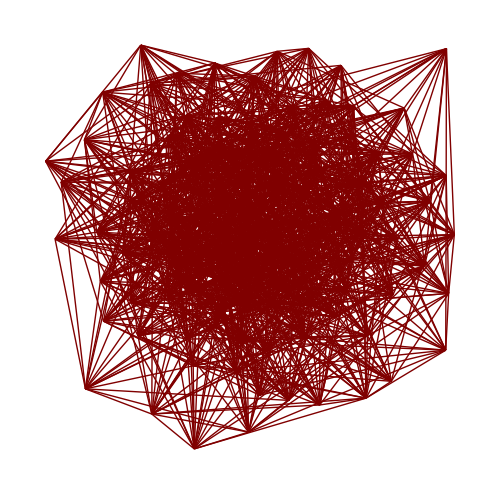

```mathematica
GraphPlot[Rule@@@(StringSplit[#,"."]&/@Keys[Flows[]]),ImageSize->500,VertexRenderingFunction->None]
```

```mathematica
BlockTimePlus[]
```

1

```mathematica
Timing[Harvest[#]&/@Keys[Flows[]];]
```

{0.07798,Null}

```mathematica
Table[Contos[ToString[c],"bala"],{c,100}]
```

{2393575482002880897049159162/41113491775332745943910645,21648000239746955542487741768729/597714885111885622539410092140,5650049173814842250172364699/152155888888856369382585720,590493574595718530619576641/21098637131784849733216120,1817475328446693074493166095191/54313399351586565388649571120,155991717884572896019838321483/6117775893187429160678869881,2584334702904509777781228959/87459147041328772289636238,102544755988695221911309/3940307790596605091664,704796719358231179815639519/31772589785858703624737895,15425785235820337234885673/790257482379499006228356,69656979729857060244536835/3132947746860733531746926,4608252849598173368/253898087162658939,868300011904141275167/38723655151158125148,479520365589919405672075/25625344579309650294504,122841393944812244276029139/6832792013598231715844964,4907377836823759511862620347/214782712380340184260652472,16571475083879112602094081380861/782968414712820566130887850864,774542365466834198581/58492246658279516082,728065064970030647003/39039740292322001232,9650291137745006105473/563126384138415401304,4452604998076872650583457/232296515682522576729444,28928103753080481140183/1664872489805403482604,9068308022952572690502781/599838638209332491429460,6689059251678146891/536539354004109456,97225857002811286549666764013/5870584942452284332922179536,41740716142113376703059/3336478695006056511912,665362111845587836278306479/41132776216556591992689264,1358700704776057413791/128009171242574748126,329278256741142009779/43607361030280929882,17137854014694978275/1468622585362729104,4445166763422181549/417827697599576880,453523121461462797739/48499328083175417448,2278966204467470400084155/140265835183610780635992,256520999055050021269/13706002693740122766,2612808300528022433351/248750427905282677374,4353735799865435/408677134231548,1304033699003513898339/93906750594229869296,678087845372610675/67913925071141968,380169256919593901/47280198147087906,1635680661361883/265212348884490,254467777506278627251589/22281460461216381300876,58250289533287851343/5361880290778806795,359483156980229/35577130217706,20740219723119601/1875384936137097,483817065/99085112,1098302303411/197852883844,103554221616800336707/9649342373830662888,73669446978982512563/8476224972542858916,90823115200871/13214971495089,10053347612021306423/1223238368994693480,33315576958156228279/3233129331397453488,15830075250851/2041814546408,785970236088431/76004537421072,6558830593/1598034357,388090018133/66457666296,79627101/19558448,730889944/253712909,6180664488065/821533409424,83406045033817/12077930184684,493249595/160831044,553875002779/129883653198,7997337199/1467827634,902000915/258030864,8538336679/1502698974,967493782565/279458391366,33633/11186,16277035/5163914,421397376797/68395619754,755/594,2612145/950011,84393/47242,8269425/3129448,20084923/6699693,6725265/3285584,299242679695/78535314352,81858375/22935359,120/97,897681695/288006192,149097/91471,10942984973/2228233560,2735/2993,6607070/1987821,1656655/895781,1978487/789360,0,40/97,1,68990/31349,553/391,7/10,100/79,629827/264422,0,0,0,0,2335/1363,0,45/47,0}

```mathematica
Total@Table[Contos[ToString[c],"bala"],{c,100}]
```

1000

```mathematica
Table[With[{is=Contos[ToString[k],"ifis"],os=Contos[ToString[k],"ofis"],h=Hint[ToString[k]]},If[EvenQ[k],h,If[Length[is]>0,RandomChoice[is],If[Length[os]>0,RandomChoice[os],0]]]],{k,Range[100]}]
```

{49.1,72.2,8.3,23.4,64.5,48.6,61.7,17.8,16.9,90.10,52.11,54.12,62.13,73.14,28.15,70.16,25.17,35.18,84.19,92.20,82.21,54.22,63.23,37.24,26.25,50.26,42.27,50.28,92.29,58.30,94.31,89.32,75.33,53.34,61.35,79.36,61.37,65.38,53.39,56.40,50.41,95.42,45.43,91.44,67.45,65.46,56.47,73.48,74.49,55.50,98.51,100.52,61.53,62.54,98.55,59.56,67.57,95.58,69.59,93.60,93.61,77.62,85.63,81.64,87.65,91.66,98.67,73.68,82.69,84.70,100.71,100.72,99.73,92.74,76.75,84.76,86.77,86.78,96.79,82.80,82.81,85.82,83.5,88.84,97.85,95.86,99.87,93.88,92.89,100.90,91.60,100.92,93.22,97.95,97.96,100.97,99.95}

```mathematica
Table[With[{is=Contos[ToString[k],"ifis"],os=Contos[ToString[k],"ofis"],h=Hint[ToString[k]]},If[EvenQ[k],h,If[Length[is]>0,RandomChoice[is],If[Length[os]>0,RandomChoice[os],0]]]],{k,Range[100]}]
```

#### Simulate all contos for 100 steps

```mathematica
Timing[cf100100=Table[(BlockTimePlus[];Table[Harvest[With[{is=Contos[ToString[k],"ifis"],os=Contos[ToString[k],"ofis"],h=Hint[ToString[k]]},If[EvenQ[k],h,If[Length[is]>0,RandomChoice[is],If[Length[os]>0,RandomChoice[os],0]]]]],{k,RandomSample[Range[100]]}];Contos[ToString[#],"bala"]&/@Range[100]),{s,100}];]
```

{26.802,Null}

#### Plots of 100 account balances for 100 steps.

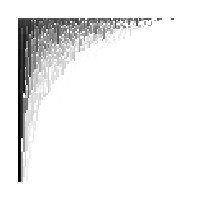
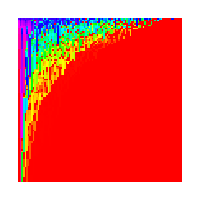
-Graphics--Graphics--Graphics-

```mathematica
Row[{ArrayPlot[N[cf100100]^.1,ImageSize->200],ArrayPlot[N[cf100100]^.1,ImageSize->200,ColorFunction->Hue],ArrayPlot[N[cf100100]^.1,ImageSize->200,ColorFunction->GrayLevel]}]
```

```mathematica
Total[Contos[ToString[#],"bala"]&/@Range[100]]
```

1000

```mathematica
cf100100
```

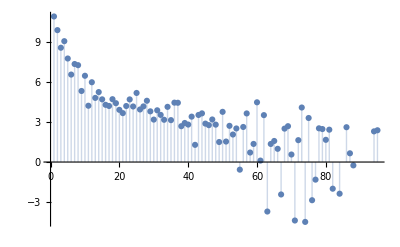

```mathematica
ListPlot[Log[Total@cf100100],Filling->Axis]
```

```mathematica
Total/@Transpose@Partition[Total@cf100100,2]
```

{6456063536842807839032428881466022256334824064124449279948748885827920586867985581388199559650484636964538430059202307690449237753603000786158566843/96715543013531329472827545833001027747849210409901728226933060056951981461095031184107823751076451666363896832019635295276236800000000000000000,3215490764510325108250325701834080518450096976865723542744557119867277559241517537022582815457160529671851253142761221837174442246396999213841433157/96715543013531329472827545833001027747849210409901728226933060056951981461095031184107823751076451666363896832019635295276236800000000000000000}

```mathematica
N[Total/@Transpose@Partition[Total@cf100100,2]]
```

{66753.1,33246.9}

#### Even contos follw hints and get most of the pie.

```mathematica
PieChart[Total/@Transpose@Partition[Total@cf100100,2]]
```

-Graphics-

```mathematica
Total[Total/@Transpose@Partition[Total@cf100100,2]]/100
```

1000

```mathematica
Row[{Dataset[Contos[]],Dataset[Flows[]]}]
```

Dataset[<>]Dataset[<>]

```mathematica
contoflowexamples
```

```mathematica
Export["contoflowexport.json",<|"contoflows"-><|"contos"->Contos[],"flows"->Flows[]|>|>,"JSON"]
```

contoflowexport.json

## Export

```mathematica
Export["contoflowexport.json",<|"contoflows"-><|"contos"->Contos[],"flows"->Flows[]|>|>,"JSON"]
```

contoflowexport.json

## 10000 contos

```mathematica
ContoFlowReset[]
```

```mathematica
Timing[Table[NewConto[ToString[n],Mod[n,2],10],{n,10000}];]
```

{0.110232,Null}

```mathematica
Timing[Table[Table[With[{rc=RandomInteger[{1,n}]},If[rc==n,Nothing,NewFlow[ToString[n],ToString[rc],RandomInteger[{1,10}]]]];,{m,20}],{n,1,10000}];]
```

{8.05389,Null}

#### Graph of Flows

```mathematica
GraphPlot3D[Rule@@@(StringSplit[#,"."]&/@Keys[Flows[]]),ImageSize->500,VertexRenderingFunction->None]
```

-Graphics3D-

#### Simulate 10000 contos for 100 steps assuming 100 harvests per step

```mathematica
Timing[cf1000100=Table[(BlockTimePlus[];Table[Harvest[With[{is=Contos[ToString[k],"ifis"],os=Contos[ToString[k],"ofis"],h=Hint[ToString[k]]},If[EvenQ[k],h,If[Length[is]>0,RandomChoice[is],If[Length[os]>0,RandomChoice[os],0]]]]],{k,RandomSample[Range[10000],100]}];Contos[ToString[#],"bala"]&/@Range[10000]),{s,100}];]
```

{46.6351,Null}

#### Plots of 10000 account balances in 100*100 array for 10 steps.

```mathematica
GraphicsGrid[Partition[ArrayPlot[Partition[#,100]]&/@cf1000100,10]]
```

-Graphics-

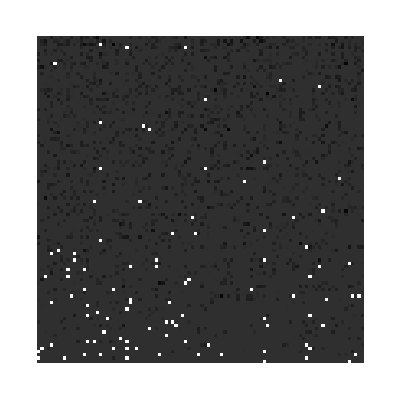

```mathematica
ArrayPlot[Partition[cf1000100[[1]],100]]
```

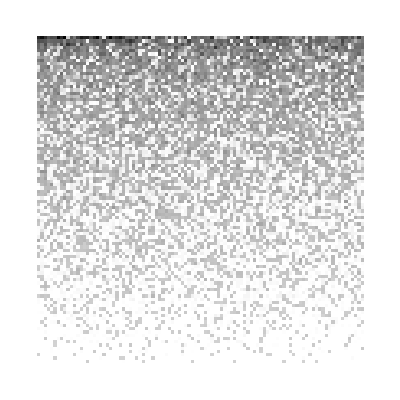

```mathematica
ArrayPlot[Partition[cf1000100[[100]],100]]
```

```mathematica
Total[Contos[ToString[#],"bala"]&/@Range[10000]]
```

100000

Larger numbers of participants requesting harvests sporadically may reduce the effect of following hints as generated with heuristics implemented in this version.

```mathematica
PieChart[Total/@Transpose@Partition[Total@cf1000100,2]]
```

-Graphics-